-3

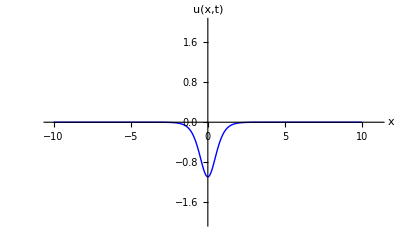

```mathematica
equation1[λ_]:=D[u[x,τ],τ]==D[u[x,τ],{x,2}]-2(λ-1/Cosh[x]^2)u[x,τ]-u[x,τ]^3
-0.5*f''[x]-6*eps*Sech[Sqrt[2*eps]*(x-0)]^2*f[x]+eps*f[x];

equation[λ_]:=D[u[x,τ],τ]==0.5*D[u[x,τ],{x,2}]+6*1*Sech[Sqrt[2*1]*(x-0)]^2*u[x,τ]-1*u[x,τ]+λ *u[x,τ]

solution[λ_,τm_,L_, initialCondition_]:=NDSolve[{equation[λ],u[-L,τ]==0,u[L,τ]==0,initialCondition},u[x,τ],{x,-L,L},{τ,0,τm}, Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->5L}}]

u[x,0]==-Sqrt[3/4]*(2*1)^(1/4)*Sech[Sqrt[2*1]*(x-0)]^2;
ls[x,0]==0.2Exp[-x^2];
uthird==-0.3*10^-4(x+10)(10-x)^3;
tmax =1000;
λ = -3

Plot[
Evaluate[u[x,τ]/.solution[λ,tmax,10,u[x,0]==-Sqrt[3/4]*(2*1)^(1/4)*Sech[Sqrt[2*1]*(x-0)]^2]/.τ->tmax ], {x, -10, 10},PlotTheme->"Classic", PlotRange->{{-10.2,11},{-2,2.}},PlotStyle->{Blue,Thick},AxesLabel->{Style[x, 16], Style[u[x,Style["t",Italic]],16]},TicksStyle->Directive[12],AxesStyle->Arrowheads[0.03],ImageSize->400]
```

```mathematica
soliton[x_,eps_]:=+6*eps*Sech[Sqrt[2*eps]*(x-0)]^2
```

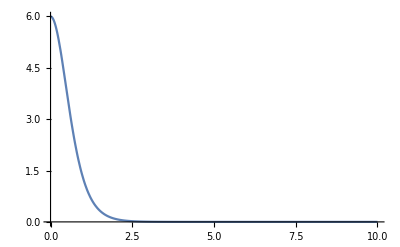

```mathematica
Plot[soliton[x,1],{x,0,10}, PlotRange->All]
```

```mathematica
Plot[u[x,0],{x,0,10}]
```

-Graphics-